# Primer programa

## Datos

```mathematica
x1= 4; (*in*)
x1p = 2;
y1p = 6;
d2=0.8;
d3 =2;
d3p = 2;
d4 = 3;
```

## Ecuaciones Cinemáticas

```mathematica
Clear[θ2,θ3,θ4,x6,θ6](*Lo que quiera borrar ira en corchetes*)
Clear[ω2,ω3,ω4,vx6,ω6]
Clear[α2,α3,α4,ax6,α6]
```

### Ecuaciones de Posición

```mathematica
u2={Cos[θ2],Sin[θ2],0};(*Para definir un conjunto de datos va entre '{}'*)
u3={Cos[θ3],Sin[θ3],0};
u4={Cos[θ4],Sin[θ4],0};
u6={Cos[θ6],Sin[θ6],0};

R1={x1,0,0};
R1p={x1p,y1p,0};
R2=d2*u2;
R3=d3*u3;
R3p=d3p*u3;
R4=d4*u4;
R6=x6*u6;

(*Lazos vectoriales*)
pos1=R1+R4-R3p-R3-R2;
pos2=R2+R3-R6-R1p;
```

```mathematica
pos1//MatrixForm (*Nos mostrara en forma matricial(solo es una imagen No operador)*)
pos2//MatrixForm
```

(3.21748-4 Cos[θ3]+3 Cos[θ4]
-0.166329-4 Sin[θ3]+3 Sin[θ4]
0.)

(-1.21748+2 Cos[θ3]-x6 Cos[θ6]
-5.83367+2 Sin[θ3]-x6 Sin[θ6]
0.)

### Ecuaciones de Velocidad

```mathematica
omega2={0,0,ω2};
omega3={0,0,ω3};
omega4={0,0,ω4};
omega6={0,0,ω6};

V1={0,0,0};
V1p={0,0,0};
V2=omega2×R2;
V3=omega3×R3;
V3p=omega3×R3p;
V4=omega4×R4;
V6=vx6*u6+omega6×R6;

(*Lazos vectoriales*)
vel1=V1+V4-V3p-V3-V2;
vel2=V2+V3-V6-V1p;
```

```mathematica
vel1//MatrixForm
vel2//MatrixForm
```

(0.+0.166329 ω2+4 ω3 Sin[θ3]-3 ω4 Sin[θ4]
0.-0.782518 ω2-4 ω3 Cos[θ3]+3 ω4 Cos[θ4]
0.)

(0.-0.166329 ω2-vx6 Cos[θ6]-2 ω3 Sin[θ3]+x6 ω6 Sin[θ6]
0.+0.782518 ω2+2 ω3 Cos[θ3]-x6 ω6 Cos[θ6]-vx6 Sin[θ6]
0.)

### Ecuaciones de aceleración

```mathematica
alfa2={0,0,α2};
alfa3={0,0,α3};
alfa4={0,0,α4};
alfa6={0,0,α6};

A1={0,0,0};
A1p={0,0,0};
A2=alfa2×R2-ω2^2*R2;
A3=alfa3×R3-ω3^2*R3;
A3p=alfa3×R3p-ω3^2*R3p;
A4=alfa4×R4-ω4^2*R4;
A6=ax6*u6+2*omega6×(vx6*u6)+alfa6×R6-ω6^2*R6;

(*Lazos Aectoriales*)
acel1=A1+A4-A3p-A3-A2;
acel2=A2+A3-A6-A1p;
```

```mathematica
acel1//MatrixForm
acel2//MatrixForm
```

(0.+0.166329 α2+0.782518 ω2^2+4 ω3^2 Cos[θ3]-3 ω4^2 Cos[θ4]+4 α3 Sin[θ3]-3 α4 Sin[θ4]
0.-0.782518 α2+0.166329 ω2^2-4 α3 Cos[θ3]+3 α4 Cos[θ4]+4 ω3^2 Sin[θ3]-3 ω4^2 Sin[θ4]
0.)

(0.-0.166329 α2-0.782518 ω2^2-2 ω3^2 Cos[θ3]-ax6 Cos[θ6]+x6 ω6^2 Cos[θ6]-2 α3 Sin[θ3]+x6 α6 Sin[θ6]+2 vx6 ω6 Sin[θ6]
0.+0.782518 α2-0.166329 ω2^2+2 α3 Cos[θ3]-x6 α6 Cos[θ6]-2 vx6 ω6 Cos[θ6]-2 ω3^2 Sin[θ3]-ax6 Sin[θ6]+x6 ω6^2 Sin[θ6]
0.)

## Solución de posición

### Solución inicial

```mathematica
Clear[θ2,θ3,θ4,x6,θ6]
Clear[ω2,ω3,ω4,vx6,ω6]
Clear[α2,α3,α4,ax6,α6]
```

```mathematica
θ2 = 180*Degree;

SolInicial = FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0},
{{θ3,25*Degree},
{θ4,85*Degree},
{θ6,260*Degree},
{x6,4.2}},MaxIterations->15](*FindRoot --> Newton_Rapson, MaxIteration -> maximo de iteraciones*)
```

{θ3→0.67246,θ4→2.1615,θ6→4.45815,x6→4.91207}

```mathematica
(θ3/.SolInicial)/Degree(*Convirtiendo de Radianes a Grados*)
(θ4/.SolInicial)/Degree
(θ6/.SolInicial)/Degree
```

38.5291

123.845

255.433

### Solución Total

```mathematica
Clear[θ2,θ3,θ4,x6,θ6]
Clear[ω2,ω3,ω4,vx6,ω6]
Clear[α2,α3,α4,ax6,α6]
```

```mathematica
θ3i=θ3/.SolInicial;
θ4i=θ4/.SolInicial;
θ6i=θ6/.SolInicial;
x6i=x6/.SolInicial;
For[i=180,i≤540,i+=1,
θ2=i*Degree;

SolPos[i]=FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0},
{{θ3,θ3i},
{θ4,θ4i},
{θ6,θ6i},
{x6,x6i}},MaxIterations->15];

θ3i=θ3/.SolPos[i];
θ4i=θ4/.SolPos[i];
θ6i=θ6/.SolPos[i];
x6i=x6/.SolPos[i];];
```

```mathematica
?SolPos;
```

Missing[UnknownSymbol,SolPos;]

## Gráficas de posición

```mathematica
tabla1=Table[{i,(θ3/.SolPos[i])/Degree},{i,180,540,1}];
tabla2=Table[{i,(θ4/.SolPos[i])/Degree},{i,180,540,1}];
tabla3=Table[{i,(θ6/.SolPos[i])/Degree},{i,180,540,1}];
tabla4=Table[{i,x6/.SolPos[i]},{i,180,540,1}];
```

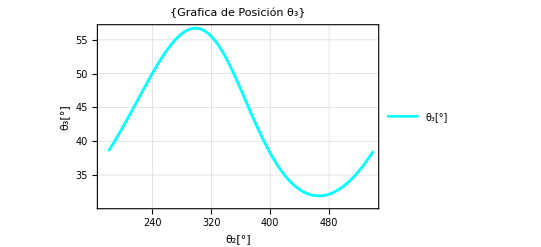

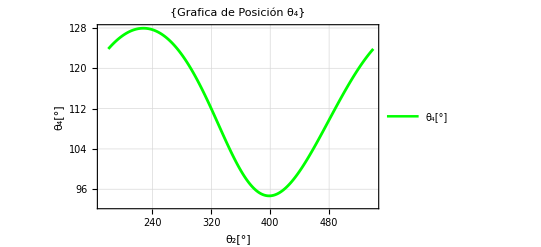

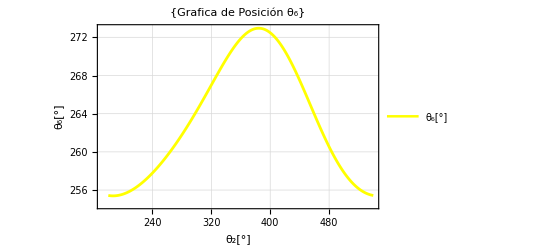

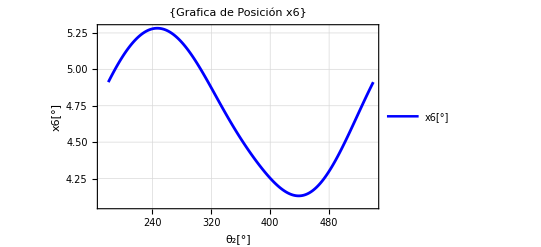

```mathematica
G1P=ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ_2[°]","θ_3[°]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición θ_3"},
PlotLegends->{"θ_3[°]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{RGBColor[0,1,1],Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ_2[°]","θ_4[°]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición θ_4"},
PlotLegends->{"θ_4[°]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{Green,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ_2[°]","θ_6[°]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición θ_6"},
PlotLegends->{"θ_6[°]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{Yellow,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
ListPlot[tabla4,
Frame->True,
FrameLabel->{"θ_2[°]","x6[°]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición x6"},
PlotLegends->{"x6[°]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{Blue,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
```

## Solución de Velocidad

```mathematica
Clear[θ2,θ3,θ4,x6,θ6]
Clear[ω2,ω3,ω4,vx6,ω6]
Clear[α2,α3,α4,ax6,α6]
```

```mathematica
ω2=12;(*rad/s*)
For[i=180,i≤540,i+=1,
θ2=i*Degree;

SolVel[i]=Solve[{
vel1⟦1⟧==0,
vel1⟦2⟧==0,
vel2⟦1⟧==0,
vel2⟦2⟧==0}/.SolPos[i],
{ω3,ω4,ω6,vx6}]//Flatten;];(*Flatten saca los elementos de un conjunto*)
```

```mathematica
SolVel[222]
```

{ω3→-2.18386,ω4→-1.83458,ω6→-0.0663478,vx6→-6.48293}

## Gráficas de Velocidad

```mathematica
tabla5=Table[{i,(ω3/.SolVel[i])},{i,180,540,1}];
tabla6=Table[{i,(ω4/.SolVel[i])},{i,180,540,1}];
tabla7=Table[{i,(ω6/.SolVel[i])},{i,180,540,1}];
tabla8=Table[{i,vx6/.SolVel[i]},{i,180,540,1}];
```

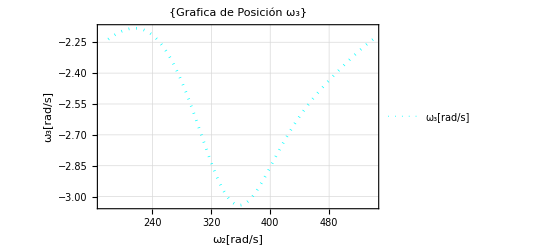

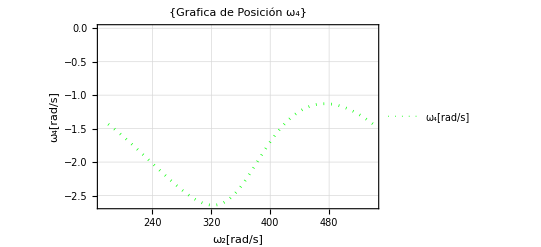

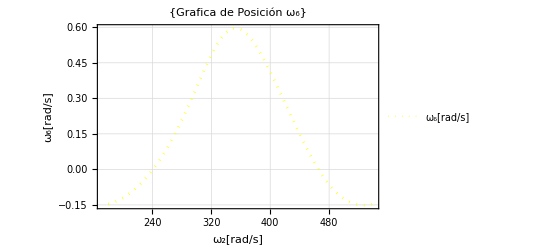

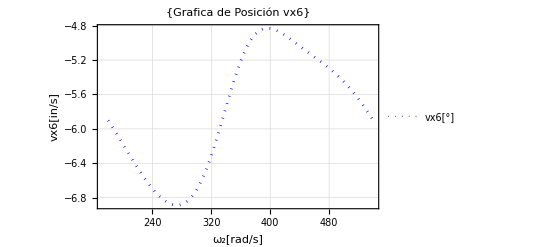

```mathematica
G1V=ListPlot[tabla5,
Frame->True,
FrameLabel->{"ω_2[rad/s]","ω_3[rad/s]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición ω_3"},
PlotLegends->{"ω_3[rad/s]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{RGBColor[0,1,1],Dotted,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
ListPlot[tabla6,
Frame->True,
FrameLabel->{"ω_2[rad/s]","ω_4[rad/s]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición ω_4"},
PlotLegends->{"ω_4[rad/s]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{Green,Dotted,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
ListPlot[tabla7,
Frame->True,
FrameLabel->{"ω_2[rad/s]","ω_6[rad/s]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición ω_6"},
PlotLegends->{"ω_6[rad/s]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{Yellow,Dotted,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
ListPlot[tabla8,
Frame->True,
FrameLabel->{"ω_2[rad/s]","vx6[in/s]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición vx6"},
PlotLegends->{"vx6[°]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{Blue,Dotted,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
```

## Solución de Aceleración

```mathematica
Clear[θ2,θ3,θ4,x6,θ6]
Clear[ω2,ω3,ω4,vx6,ω6]
Clear[α2,α3,α4,ax6,α6]
```

```mathematica
ω2=12;
α2=0;
For[i=180,i≤540,i+=1,
θ2=i*Degree;

SolAcel[i]=Solve[{
acel1⟦1⟧==0,
acel1⟦2⟧==0,
acel2⟦1⟧==0,
acel2⟦2⟧==0}/.SolVel[i]/.SolPos[i],
{α3,α4,α6,ax6}]//Flatten;];(*Flatten saca los elementos de un conjunto*)
```

```mathematica
?SolAcel
```

## Gráficas de Aceleración

```mathematica
tabla9=Table[{i,(α3/.SolAcel[i])},{i,180,540,1}];
tabla10=Table[{i,(α4/.SolAcel[i])},{i,180,540,1}];
tabla11=Table[{i,(α6/.SolAcel[i])},{i,180,540,1}];
tabla12=Table[{i,ax6/.SolAcel[i]},{i,180,540,1}];
```

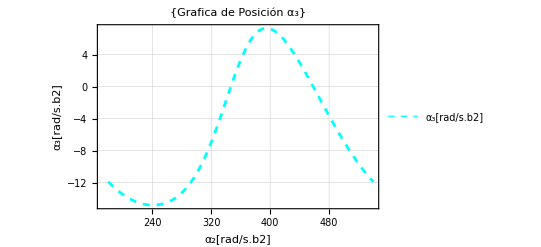

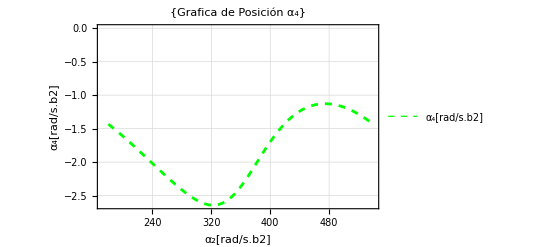

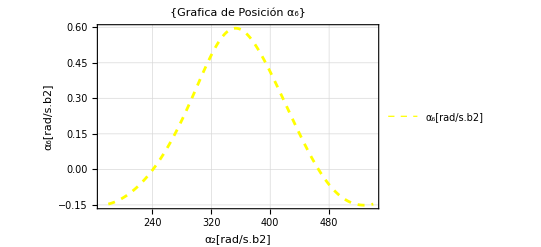

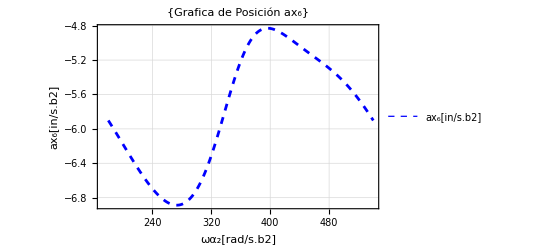

```mathematica
G1A=ListPlot[tabla9,
Frame->True,
FrameLabel->{"α_2[rad/s.b2]","α_3[rad/s.b2]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición α_3"},
PlotLegends->{"α_3[rad/s.b2]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{RGBColor[0,1,1],Dashed,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
ListPlot[tabla6,
Frame->True,
FrameLabel->{"α_2[rad/s.b2]","α_4[rad/s.b2]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición α_4"},
PlotLegends->{"α_4[rad/s.b2]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{Green,Dashed,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
ListPlot[tabla7,
Frame->True,
FrameLabel->{"α_2[rad/s.b2]","α_6[rad/s.b2]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición α_6"},
PlotLegends->{"α_6[rad/s.b2]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{Yellow,Dashed,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
ListPlot[tabla8,
Frame->True,
FrameLabel->{"ωα_2[rad/s.b2]","ax_6[in/s.b2]"},(*Control + - =Subindice*)
PlotLabel->{"Grafica de Posición ax_6"},
PlotLegends->{"ax_6[in/s.b2]"},(*Nos Pone como se ve cierta grafica*)
Joined->True,    (*Joined-> Une todos los puntos de mi grafica*)
GridLines->Automatic,
PlotStyle->{Blue,Dashed,Thickness[.005]},(*Dot or Dasheed son para puntos o rayas hasta su combinacion*)
ImageSize->400
]
```

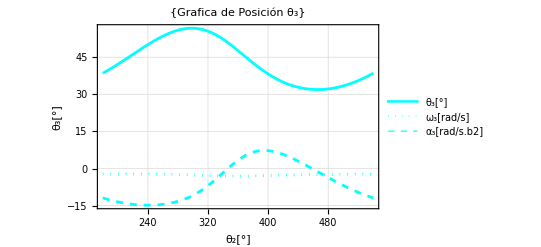

```mathematica
Show[G1P,G1V,G1A,PlotRange->All](*Me muestra todo en un solo cuadro*)
(*PlotRange->All Me va mostrar el rango total de todas las gráficas*)PlotRange->All
```

## Simulación

```mathematica
Clear[θ2,θ3,θ4,x6,θ6]
Animate[
θ2=i*Degree;

k={0,0,1};
cero={0,0,0};(*Vector cero*)
(*-----DEFINIENDO GEOMETRICAMENTE-----*)

eslabon2=Cylinder[{cero,R2},0.1];(*{inicio,final}, radio del cilindro*)
eslabon3=Cylinder[{R2+0.4*k,R1+R4+0.4*k},0.1]/.SolPos[i]; (*Se movera 0.4 hacia enfrente*)
eslabon4=Cylinder[{R1,R1+R4},0.1]/.SolPos[i];
eslabon5=Cylinder[{R1p+R6+0.5*u6+0.8*k,R1p+R6-0.5*u6+0.8*k-0.5*u6},0.2]/.SolPos[i];(*corredera*)
eslabon6=Cylinder[{R1p+0.8*k,R1p+5.5*u6+0.8*k},0.1]/.SolPos[i];

ejeA=Cylinder[{-0.2*k,0.2*k},0.15];
ejeB=Cylinder[{R2-0.2*k,R2+0.6*k},0.15];
ejeC=Cylinder[{R1+R4-0.2*k,R1+R4+0.6*k},0.15]/.SolPos[i];
ejeD=Cylinder[{R1-0.2*k,R1+0.2*k},0.15];
ejeE=Cylinder[{R1p-0.2*k,R1p+k},0.15];
ejeF=Cylinder[{R1p+R6+0.2*k,R1p+R6+1.1*k},0.15]/.SolPos[i];
                                                (*-----CARACTERISTICAS-----*)
barra2=Graphics3D[{Purple,eslabon2}];
barra3=Graphics3D[{Green,eslabon3}];
barra4=Graphics3D[{Blue,eslabon4}];
corredera5=Graphics3D[{Cyan,eslabon5}];
barra6=Graphics3D[{Pink,eslabon6}];

pernoA=Graphics3D[{Black,ejeA}];
pernoB=Graphics3D[{Black,ejeB}];
pernoC=Graphics3D[{Black,ejeC}];
pernoD=Graphics3D[{Black,ejeD}];
pernoE=Graphics3D[{Black,ejeE}];
pernoF=Graphics3D[{Black,ejeF}];

Show[barra2,barra3,barra4,corredera5,barra6,pernoA,pernoB,pernoC,pernoD,pernoE,pernoF,
Axes->True,
AspectRatio->1,
AxesLabel->{"X [in]","Y [in]","Z [in]"},
ImageSize->400,
ViewVertical->{0,1,0},
ViewPoint->{0,0,Infinity},
PlotRange->{{-5,10},{-2,7},{-1,1.3}}
],{i,180,540,1},AnimationRunning->False]
```